```mathematica
<<SymbolicComputing`
$Version
$SCVersion
DateString[]
```

11.3.0 for Linux x86 (64-bit) (March 7, 2018)

5.0.4 (August 5, 2018)

Fri 9 Nov 2018 13:31:16

## References

W. E. Boyce and R. C. DiPrima, Elementary Differential Equations and Boundary Value Problems, 10th ed. Wiley, 2012.

## 9.4 Competing Species

Let x and y be the populations of the two species at time t.

```mathematica
{ⅆx/ⅆt==x(1-x-y),ⅆy/ⅆt==y(0.75-y-0.5x)}(*eq3*)
SCMAF[%,RA,{All,{ⅆx_/ⅆt==0}},
SCSolve,{All,{x,y}},
Thread,{All,Equal},Level->{1},
Thread,{All,Equal},Take->{2},IgnoreError->True]
```

{ⅆx/ⅆt==x (1-x-y),ⅆy/ⅆt==(0.75-0.5 x-y) y}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x,y}=={0.,0.75},{x,y}=={0.5,0.5},{x,y}=={1.,0.},{x,y}=={0.,0.}}

{{0.,0.75},{0.5,0.5},{1.,0.},{0.,0.}}

{ⅆx/ⅆt==x (1-x-y),ⅆy/ⅆt==(0.75-0.5 x-y) y}

{ⅆx/ⅆt,ⅆy/ⅆt}=={x (1-x-y),(0.75-0.5 x-y) y}

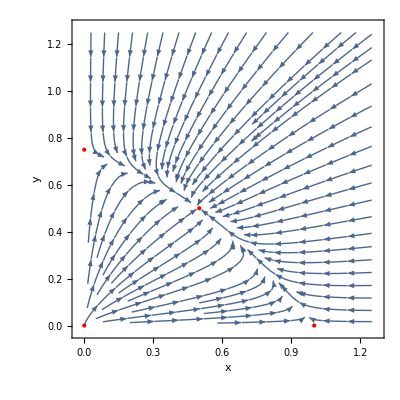

```mathematica
{ⅆx/ⅆt==x(1-x-y),ⅆy/ⅆt==y(0.75-y-0.5x)}(*eq3*)
SCMAF[%,Thread,{All,Equal},
StreamPlot,{At[2],{x,0,1.25},{y,0,1.25},Epilog->{Red,Point@{{0.,0.75},{0.5,0.5},{1.,0.},{0.,0.}}}, FrameLabel->{x,y}},Take->{2}]
```

The Jacobian matrix is

```mathematica
J==({{(∂F)/(∂x), (∂F)/(∂y)}, {(∂G)/(∂x), (∂G)/(∂y)}})
SCMAF[%,RA,{At[2],{F==x(1-x-y),G==y(0.75-y-0.5x)}(*eq6*)},Post->SCDerivExpand,
ExpandAll,At[2],MatrixForm->True](*eq7*)
```

J=={{(∂F)/(∂x),(∂F)/(∂y)},{(∂G)/(∂x),(∂G)/(∂y)}}

J=={{1-2 x-y,-x},{-0.5 y,0.75-0.5 x-2. y}}

J==(1-2 x-y | -x
-0.5 y | 0.75-0.5 x-2. y)

x=0, y=0

```mathematica
J==({{1-2 x-y, -x}, {-0.5 y, 0.75-0.5 x-2. y}})
SCMAF[%,RA,{At[2],{x==0,y==0}}]
```

J=={{1-2 x-y,-x},{-0.5 y,0.75-0.5 x-2. y}}

J=={{1,0},{0.,0.75}}

```mathematica
SCARA[Eigensystem[J],J=={{1,0},{0.,0.75}}]
```

Eigensystem[J]=={{1.,0.75},{{-1.,0.},{0.,-1.}}}

So the general solution of the system is

```mathematica
({{x}, {y}})==Subscript[c, 1]({{-1}, {0}})ⅇ^t+Subscript[c, 2]({{0}, {1}})ⅇ^(0.75t);(*eq10*)
```

x=1, y=0

```mathematica
J==({{1-2 x-y, -x}, {-0.5 y, 0.75-0.5 x-2. y}})
SCMAF[%,RA,{At[2],{x==1,y==0}},
Eigensystem,All,Level->{1}]
```

J=={{1-2 x-y,-x},{-0.5 y,0.75-0.5 x-2. y}}

J=={{-1,-1},{0.,0.25}}

Eigensystem[J]=={{-1.,0.25},{{1.,0.},{-0.624695,0.780869}}}

So the general solution of the system is

```mathematica
({{x}, {y}})==Subscript[c, 1]({{1}, {0}})ⅇ^-t+Subscript[c, 2]({{-0.624695}, {0.780869}})ⅇ^(0.25t);(*eq13*)
```

x=0, y=0.75

```mathematica
J==({{1-2 x-y, -x}, {-0.5 y, 0.75-0.5 x-2. y}})
SCMAF[%,RA,{At[2],{x==0,y==0.75}},
Eigensystem,All,Level->{1}]
```

J=={{1-2 x-y,-x},{-0.5 y,0.75-0.5 x-2. y}}

J=={{0.25,0},{-0.375,-0.75}}

Eigensystem[J]=={{-0.75,0.25},{{0.,1.},{0.936329,-0.351123}}}

So the general solution of the system is

```mathematica
({{x}, {y}})==Subscript[c, 1]({{0}, {1}})ⅇ^(-0.75t)+Subscript[c, 2]({{0.936329}, {-0.351123}})ⅇ^(0.25t);(*eq16*)
```

x=0.5, y=0.5

```mathematica
J==({{1-2 x-y, -x}, {-0.5 y, 0.75-0.5 x-2. y}})
SCMAF[%,RA,{At[2],{x==0.5,y==0.5}},
Eigensystem,All,Level->{1}]
```

J=={{1-2 x-y,-x},{-0.5 y,0.75-0.5 x-2. y}}

J=={{-0.5,-0.5},{-0.25,-0.5}}

Eigensystem[J]=={{-0.853553,-0.146447},{{0.816497,0.57735},{0.816497,-0.57735}}}

So the general solution of the system is

```mathematica
({{x}, {y}})==Subscript[c, 1]({{0.816497}, {0.57735}})ⅇ^(-0.853553t)+Subscript[c, 2]({{0.816497}, {-0.57735}})ⅇ^(-0.146447t);(*eq19*)
```